## Recurrence Quantification Analysis

An analysis method for dynamical systems.

Flip Phillips
Skidmore College Vision Laboratories
© 2015-9

## Introduction

Recurrence Quantification Analysis or RQA is a technique for understanding real-world dynamical systems. It consists of three main steps:

Dimensional re-embedding (not strictly a part of the technique, but frequently practiced)

Recurrence map generation

Quantification of map features

## Examples

### Preliminaries

Load the package:

```mathematica
<<RQA`
```

If you’d like to see what is there —

```mathematica
?RQA`*
```

### Data

We generate a Henon attractor as example:

```mathematica
α=1.4;β=0.3;nMax=2000;settle=40;
```

```mathematica
henonxy=
Drop[RecurrenceTable[{x[n+1]==1-α x[n]^2+y[n],
y[n+1]==β x[n],x[0]==0.0,y[0]==0.0},{x,y},{n,1,nMax+settle},DependentVariables->{x,y}],settle];
```

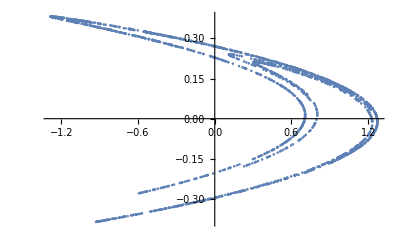

```mathematica
ListPlot[henonxy]
```

### Time Series

The RQA package uses the Wolfram Language TimeSeries as its data structure. This is primarily since the analysis our lab has used has been in the time domain. Obviously, RQA is not limited to temporal dynamics, so this is a bit of a compromise that creates a class of parametric function in one variable. Future versions might (well, do in our local stuff) support other parameterizations, multidimensional in nature:

```mathematica
hts=TimeSeries[TemporalData[henonxy,{1,Automatic,1},ValueDimensions->2]]
```

TimeSeries[…]

Let’s use an interesting, 200-wide, window:

```mathematica
tStart=1001;
w=200;
```

```mathematica
hw=TimeSeriesWindow[hts,{tStart,tStart+w-1}]
```

TimeSeries[…]

Make a 1D, x-only version looking at just the changes of the x-variable:

```mathematica
hx=TimeSeries[TemporalData[hw["Values"][[All,1]],{tStart,tStart+w-1,1}]]
```

TimeSeries[…]

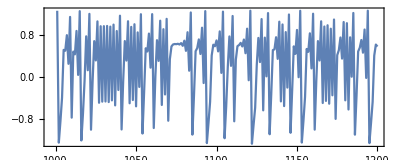

```mathematica
ListLinePlot[hx,Axes->None,Frame->True,AspectRatio->.4]
```

The TimeSeries here assumes a time-step of 1 is equal to an iteration of the attractor. Obviously we are not limited to integer steps or even discrete, equally spaced data. The TimeSeries structure allows us to do all sorts of re-sampling and approximation of the raw data.

### Embedding

The RQA package has some tools for estimating proper embedding dimension and lag. For now, we’ll simply embed our data into 3 dimensions with a lag/τ of 1.0:

```mathematica
hxe3=RQAEmbed[hx,3,1.0]
```

TimeSeries[…]

This shows how the x-coordinate jumps back and forth over time but within the pattern of the attractor:

```mathematica
ParametricPlot3D[hxe3[t],{t,1001,1198}]
```

-Graphics3D-

### Distance Map

The first step is to create a distance map of the system. This map is a representation of how the system transitions at each time step. Here a basic unscaled distance map from the above embedding, using EuclideanDistance as a metric:

```mathematica
dm=RQADistanceMap[hxe3,DistanceFunction->EuclideanDistance];
```

You can use any distance function you’d like. By default, SquaredEuclideanDistance is used. There are also rescaling options.

```mathematica
ArrayPlot[dm,DataReversed->True,PlotLegends->Automatic,FrameTicks->None,ColorFunction->ColorData["Temperature"],ImageSize->500,FrameLabel->{"time","time",None,None}]
```

-Graphics-

The distance map shows distance between a given timestep and all other timesteps during the evolution of the system. In this presentation the x and y axes are increasing t from the lower left. The diagonal is called the LOI or Line of Identity and is always 0 since it is the distance between a point at time t and itself at time t.

Note also that, for many systems, this map will be symmetric about the diagonal due to  ‖p_i-p_j‖==‖p_j-p_i‖ transitivity of real metrics. Prior versions of the RQA package (before 0.3.0) did not take this into account, but later versions do. This problem is not well ‘solved’ but there is significant research in the area [refXXX].

Also note that distance maps need not be generated by the RQA package. Any square matrix of distances can be used. It is, of course, up to you to make sure that the map is valid / meaningful.

### Recurrence Map

Recurrence maps can be generated from two sources — 1) the raw time series, in which case a temporary distance map is generated and destroyed in the process, or 2) from an existing distance map. The former is simpler for quick analyses, the latter for exploration since it doesn’t require the map to be re-computed every time a recurrence map is needed.

Here' s a recurrence map, computed from an ‘on the fly’ Euclidean distance map, distances linearly rescaled to [0,1], with a distance threshold of 0.03 / 3%:

```mathematica
rm=RQARecurrenceMap[hxe3,0.03,"Rescale"->True,DistanceFunction->EuclideanDistance]
```

SparseArray[…]

Notice that this returns a SparseArray object for space savings and other computational advantages. We can visualize it:

```mathematica
ArrayPlot[rm,DataReversed->True,FrameTicks->None,ImageSize->500,PlotLegends->Automatic]
```

-Graphics-

We can also use the previously computed map for efficiency. Here is an interactive example:

```mathematica
Manipulate[ArrayPlot[RQARecurrenceMap[dm,ϵ],DataReversed->True,FrameTicks->None,ImageSize->500,PlotLegends->None],{{ϵ,0.05*Subtract@@Reverse[mm=MinMax[RQANonzeroValues[dm]]]},Sequence@@mm},SaveDefinitions->True]
```

Notice that, since the distance map dm is unscaled, we need to describe a different set of controls / thresholds to Manipulate.

Essentially, a recurrence plot indicates locations that, over time, remain within some (usually small) distance. The various structures indicate different properties of the evolving system, namely:

Homogeneity - The process is stable.

Density change in the LL or UR - The process is nonstationary or in transition between states.

White (0) banding - The process is nonstationary with some rare or transitional states.

Periodic patterns - The process has periodic behavior.

Isolated points - The process is dominated by large transitions or may be stochastic.

Diagonal lines parallel to LOI - The process is deterministic in the periodic sense (long lines) or chaotic sense (short lines)

Diagonal lines orthogonal to the LOI - The process is time-reversed or palindromic.

Vertical and horizontal lines and rectangles - The process is ‘laminar’ or stuck.

— From Webber & Zbilut, 2005.

The goal of the following measurements is to describe these qualities in a systematic, quantitative way.

### RQA Measurements

So - called ‘classical’ RQA consists of a handful of descriptive measures based primarily on the diagonal features of the recurrence map.

#### Recurrence

Recurrence (aka REC) measures the density of recurrent locations. It describes the relative sparseness of the recurrence map. Small numbers approaching 0 suggest sparseness, numbers approaching 1, denseness.

```mathematica
RQARecurrence[rm]//N
```

0.0165616

The RQA package computes exact values for these ratios:

```mathematica
RQARecurrence[rm]
```

323/19503

but it is frequently easier to understand these numerically. In early literature, these values were expressed in percentages, so it is advisable to be aware of this.

#### Determinism

Determinism (DET) is defined as the fraction of points that lie along diagonal lines. The more deterministic the system, the higher this value, on a range of [0,1] :

```mathematica
RQADeterminism[rm]//N
```

0.873065

Strictly speaking, the determinism of the system here is bounded by an optional parameter, D_min, that specifies the shortest segment that is to be counted as a predictor. By default, D_min=2 so this specifies the shortest possible ‘line’ in the recurrence plot. Different values can be specified via an option “Dmin”:

```mathematica
RQADeterminism[rm,"Dmin"->4]//N
```

0.575851

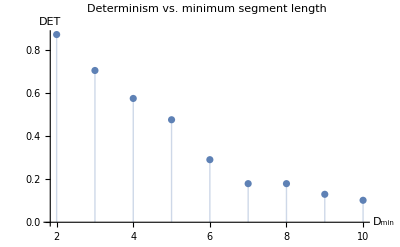

```mathematica
ListPlot[Table[{d,RQADeterminism[rm,"Dmin"->d]},{d,2,10}],Filling->Bottom,AxesLabel->{"D_min","DET"},PlotLabel->"Determinism vs. minimum segment length"]
```

Intuitively, as the criterion for ‘line-ness’ increases, the determinism decreases. For D_min=1 DET is 1, since all recurrent points are ‘segments’

```mathematica
RQADeterminism[rm,"Dmin"->1]
```

1

#### Ratio

The ratio of REC and DET provides a way of detecting certain transitions. In these cases REC will decrease while the DET remains constant. For our henon data:

```mathematica
RQARatio[rm]//N
```

52.7164

so, for a minimum segment length of D_min=2 the DET is much higher than the REC. Increasing D_min gives us, again, what we’d expect:

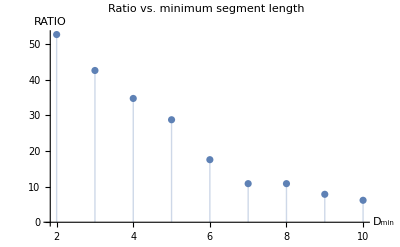

```mathematica
ListPlot[Table[{d,RQARatio[rm,"Dmin"->d]},{d,2,10}],Filling->Bottom,AxesLabel->{"D_min","RATIO"},PlotLabel->"Ratio vs. minimum segment length"]
```

#### D_max

D_max is simply the longest diagonal. The smaller the D_max, the more divergent the trajectories.

```mathematica
RQADmax[rm]
```

12

#### ⟨D⟩

The average diagonal length, ⟨D⟩ or D_mean gives the average time two segments are apart:

```mathematica
RQADmean[rm]//N
```

3.86301

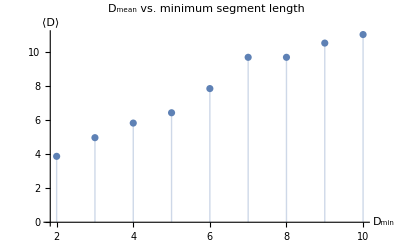

```mathematica
ListPlot[Table[{d,RQADmean[rm,"Dmin"->d]},{d,2,10}],Filling->Bottom,AxesLabel->{"D_min","⟨D⟩"},PlotLabel->"D_mean vs. minimum segment length"]
```

#### Trend

```mathematica
RQATrend[rm,"NTruncate"->Automatic,"Dmin"->2]//N
```

0.00869476

#### Entropy

```mathematica
RQAEntropy[rm]//N
```

1.58496

#### Laminarity

```mathematica
RQALaminarity[rm]
```

1/646 RQANVerticalRecurrentPoints[SparseArray[…],2]

```mathematica
s
```

#### Trapping time

```mathematica
RQATrappingTime[rm,2]//N
```

Mean[RQAVerticalLineLengths[SparseArray[…],2.]]

```mathematica
RQAVmax[rm]
```

7

```mathematica
RQAChaos[rm]//N
```

0.0833333

## References

Webber Jr, C. L., & Zbilut, J. P. (2005). Recurrence quantification analysis of nonlinear dynamical systems. Tutorials in contemporary nonlinear methods for the behavioral sciences, 94, 26-94. https://www.nsf.gov/pubs/2005/nsf05057/nmbs/chap2.pdf

## End Matter

### Acknowledgements

• I was introduced to RQA for eye tracking, somewhat skeptically, by Jeff Pelz of RIT.
• The original package was developed with my student Dave ‘CORM’ Jacobs for work on eye tracking trajectory analysis.
• The package was further developed for use by Alison Ord as part of the 2019 Wolfram Summer School. Code contributions from Paul Abbott.
• Even though retired, Charles Webber has graciously offered to help clean some of the dust out of this mess.

### Notes

Much can be learned from —

Webber Jr, C. L., & Zbilut, J. P. (2005). Recurrence quantification analysis of nonlinear dynamical systems. Tutorials in contemporary nonlinear methods for the behavioral sciences, 94, 26-94. https://www.nsf.gov/pubs/2005/nsf05057/nmbs/chap2.pdf

This chapter is from a collection on the subject of nonlinear methods, Tutorials in contemporary nonlinear methods for the behavioral sciences, written for the NFS and edited by Michael Riley and Guy Van Orden. https://nsf.gov/pubs/2005/nsf05057/nmbs/nmbs.pdf

Guy passed away from pancreatic cancer a few years after I met him. He was a super nice, encouraging, and helpful person. If you use this package and feel the need to pay-it-forward somehow, consider dropping a few bucks to a cancer charity or the NSF or NIH.